```mathematica
SetDirectory["L:/moose/project2/trunk/elk/tests/richards/user_objects"];ClearAll[th,thprime,th2prime];th = th/.First[Solve[pc/las==(1-th)/th+(1/cc)Log[(cc-th)/((cc-1)th)],th]];
thprime = D[th,pc];
th2prime = D[th,{pc,2}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

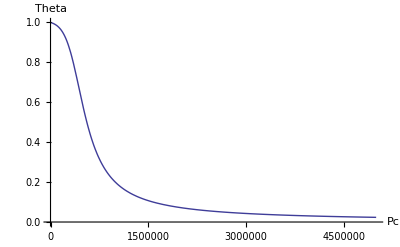

```mathematica
Plot[th/.{cc->1.01,las->10^5},{pc,0,5*10^6},AxesLabel->{"Pc","Theta"},PlotRange->{0,1}]
```

```mathematica
ClearAll[satBW,satBWprime, satBW2prime];
satBW[pc_]= th/.{cc->1.01,las->10^5};
satBWprime[pc_] = D[th,pc]/.{cc->1.01,las->10^5};
satBW2prime[pc_] = D[th,{pc,2}]/.{cc->1.01,las->10^5};
```

```mathematica
Export["satBW.csv",{#,satBW[-#]}&/@Range[-5*10^6,0,10^4],"Table"];
Export["satBWprime.csv",Join[{#,-satBWprime[-#]}&/@Range[-5*10^6,0,10^4],{{1,0}}],"Table"];
Export["satBW2prime.csv",Join[{#,satBW2prime[-#]}&/@Range[-5*10^6,0,10^4],{{1,0}}],"Table"];
```